-Graphics-

Obvod je napájen střídavým zdrojem napětí uZ (t) = amplituda*sin (2*π*f*t+2.1), kde amplituda je 5 V a frekvence f = 100 Hz . Hodnoty součástek jsou R1 = 10 kΩ, R2 = 10 kΩ,  L1 = 56 μH.  Vyřešte :
	1. Uvedený zdroj převeďte na fázor uZf a řešte obvod v HUSu . (DU3d - 1 bod)
	2. Spočtěte přenos obvodu a zobrazte jej v grafu pro ω = (10^7,10^12). (DU3e - 1bod)
	3. Za předpokladu že uZ = 5 V převeďte obvod do stejnosměrného stavu a vypočtěte napětí uout . 	(DU3e - 1 bod)(DU3f - 1 bod do aktivity)

{ω→200 π}

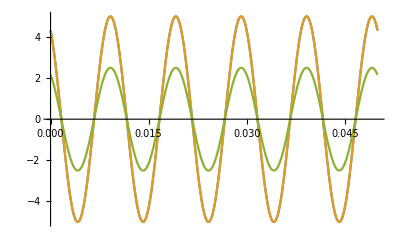

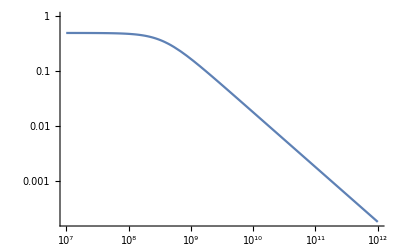

```mathematica
ClearAll["Global`*"]

amplituda = 5;
frekvence = 100;
perioda=1/frekvence;
tmax=5*perioda;
omega={ω->2*π*frekvence}
in= amplituda*Sin[ω*t+2.1] /. omega;
uZf = amplituda*ⅇ^(ⅉ*2.1);

Plot[Im[uZf * ⅇ^(ⅉ*ω*t)/.omega], {t, 0, tmax}];

rovnice ={
0==iuZ+iL1,
iL1==iR1,
iR1==iR2,

uZf==u1,
u1-u2==ⅉ*ω*L1*iL1,
u2-u3==R1*iR1,
u3==R2*iR2,
uOut==u3
};

nezname = {iuZ, iR1, iR2, iL1, u1, u2, u3, uOut};
soucastky = {R1->10*10^3, R2->10*10^3, L1->56*10^-6};

reseni = Solve[rovnice/.soucastky, nezname];

Plot[{Im[(u1/.reseni)*ⅇ^(ⅉ*ω*t)/.omega], Im[(u2/.reseni)*ⅇ^(ⅉ*ω*t)/.omega], Im[(u3/.reseni)*ⅇ^(ⅉ*ω*t)/.omega]},{t,0,tmax} ]

prenos = u3/u1/.reseni[[1]];
LogLogPlot[Abs[prenos], {ω,10^7, 10^12}]
```

```mathematica
ClearAll["Global`*"]

uZ=5;
R1=10*10^3;
R2=10*10^3
R12=R1+R2;

uout = uZ*R2/R12//N;
```

10000